```mathematica
(*Transforma tensor vetorial de voigth em tensor  3x3*)
FromVoigtToCart[sig_]:={{sig[[1]],sig[[6]],sig[[5]]},{sig[[6]],sig[[2]],sig[[4]]},{sig[[5]],sig[[4]],sig[[3]]}}
(*Transforma tensor  3x3 em tensor vetorial de voigth *)
FromCartToVoigt[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],sig[[2,3]],sig[[1,3]],sig[[1,2]]}
FromCartToVoigt2[sig_]:={sig[[1,1]],sig[[2,2]],sig[[3,3]],2sig[[2,3]],2sig[[1,3]],2sig[[1,2]]}
ComputeS[m_]:=Block[{cart,Sint},
cart=FromVoigtToCart[m];
Sint=cart-1/3 Tr[cart]IdentityMatrix[3];
FromCartToVoigt2[Sint]
]
ComputeJ2[m_]:=Block[{cart,S},
cart=FromVoigtToCart[m];
S=cart-1/3 Tr[cart]IdentityMatrix[3];
1/2. Tr[S.S]
]
ComputeI1[m_]:=Block[{cart,S},
cart=FromVoigtToCart[m];
N[Tr[cart]]
]
P={{2/3,-1/3,-1/3,0,0,0},{-1/3,2/3,-1/3,0,0,0},{-1/3,-1/3,2/3,0,0,0},{0,0,0,2,0,0},{0,0,0,0,2,0},{0,0,0,0,0,2}}//N;
ax[sigma_]:=A/3 {1,1,1,0,0,0}+1/(2Sqrt[ComputeJ2[sigma]])ComputeS[sigma]//.subst2
dadsigmax[sigma_]:=P 1/(2 Sqrt[ComputeJ2[sigma]])-1/(4 ComputeJ2[sigma]^(3/2))Outer[Times,ComputeS[sigma],ComputeS[sigma]]
(*Calcula autovalores e autovetores e ordena na ordem decrescente*)
EigenSystem[m_]:=Block[{epstprincipalvals,epstprincipaldir,orderedvalues,index,oderedvectors,cart},
cart=FromVoigtToCart[m];
{epstprincipalvals,epstprincipaldir}=Eigensystem[cart//N];
orderedvalues=Sort[epstprincipalvals,Greater];
index=DeleteDuplicates[Table[Position[epstprincipalvals,orderedvalues[[i]]],{i,1,3}]//Flatten];
oderedvectors=Table[epstprincipaldir[[index[[i]]]],{i,1,3}];
{orderedvalues,oderedvectors}
]
HW[{xi_,rho_,beta_}]:=Block[{sig1,sig2,sig3},
sig1=xi /Sqrt[3]+Sqrt[2/3]rho Cos[beta];
sig2=xi/Sqrt[3] +Sqrt[2/3]rho Cos[beta-2Pi/3];
sig3=xi/Sqrt[3] +Sqrt[2/3] rho Cos[beta+2Pi/3];
N[{sig1,sig2,sig3}]
];

F1HWCylDruckerPrager[{xi_,rho_,beta_}]:=Block[{xiint,rhoint,betaint,sigy,A,B,c},
xiint=xi;
rhoint=Sqrt[2] (B c-A xi);
rhoint=√2 B c-√(2/3) A xi;
betaint=beta;
N[{xiint,rhoint,betaint}]
]
FDP[I1_,J2_]:=(Sqrt[J2]+A I1/3 -c B)
ApplyStrainComputeSigmaDep[epst_,epsp_,subst2_]:=Block[{invCe,R,Q,invQ,sig1,sig2,sig3,epse2D,sz,nu,ex,ey,exy,sx,sy,tauxy,sigproj2D,Dep2D,sn1,pn1,updatedstress,II,eq,c ,B,A,solgamma,full,dgamma,acone,yield,I1,J2,sol,d,Dep,CT,T,epse,gamma,epsetrial,sigprojvoigth,proj,asol,dadsigg,THWR,Rot,xitrial,xisol,xi,beta,rho,sigma,rhotrial,Ce,pt,vec,betasol,young,G,K,epstint,epspint},

Ce=N[{{(4 G)/3+K,-(2 G)/3+K,-(2 G)/3+K,0,0,0},{-(2 G)/3+K,(4 G)/3+K,-(2 G)/3+K,0,0,0},{-(2 G)/3+K,-(2 G)/3+K,(4 G)/3+K,0,0,0},{0,0,0,G,0,0},{0,0,0,0,G,0},{0,0,0,0,0,G}}]//.subst2;
invCe=N[{{(G+3 K)/(9 G K),-1/(6 G)+1/(9 K),-1/(6 G)+1/(9 K),0,0,0},{-1/(6 G)+1/(9 K),(G+3 K)/(9 G K),-1/(6 G)+1/(9 K),0,0,0},{-1/(6 G)+1/(9 K),-1/(6 G)+1/(9 K),(G+3 K)/(9 G K),0,0,0},{0,0,0,1/G,0,0},{0,0,0,0,1/G,0},{0,0,0,0,0,1/G}}]//.subst2;

epstint={epst[[1]],epst[[2]],0,0,0,epst[[3]]}//N;
epspint={epsp[[1]],epsp[[2]],0,0,0,epsp[[3]]}//N;

epsetrial=(epstint-epspint);

sigma=Ce.epsetrial;

I1=ComputeI1[sigma];
J2=ComputeJ2[sigma];
yield=FDP[I1,J2]//.subst2;

If[yield<0,
sigprojvoigth=sigma;
epse=epsetrial;
Dep=Ce;
gamma=0;
,

xitrial=I1/Sqrt[3];
rhotrial=Sqrt[2J2];

(*Auto valores em ordem decrescente*)
{pt,vec}=EigenSystem[sigma]//N;

betasol=ArcTan[(√3 (-sig2+sig3))/(-2 sig1+sig2+sig3)]//.subst2/.{sig1->pt[[1]],sig2->pt[[2]],sig3->pt[[3]]};
xisol=1/(6 (G+A^2 K))(-3 A K (2 sig1-sig2-sig3) Cos[betasol]+√3 (6 A B c K+2 G (sig1+sig2+sig3)-3 A K (sig2-sig3) Sin[betasol]))//.subst2/.{sig1->pt[[1]],sig2->pt[[2]],sig3->pt[[3]]};
proj=HW[F1HWCylDruckerPrager[{xisol,rho,betasol}]]//.subst2;
sigprojvoigth=FromCartToVoigt[Sum[proj[[i]] Outer[Times,vec[[i]],vec[[i]]],{i,1,3}]];
asol=ax[sigprojvoigth]//.subst2;
dadsigg=dadsigmax[sigprojvoigth]//.subst2;
epse=invCe.sigprojvoigth;
gamma=Norm[epsetrial-epse]/Norm[asol];

dadsigg=dadsigmax[sigma]//.subst2;
CT=Ce.((IdentityMatrix[6]-(Outer[Times,asol,asol].Ce)/(asol.Ce.asol)));
T=(IdentityMatrix[6]- gamma dadsigg.Ce );
Dep=CT.T;

acone=Sqrt[J2]-gamma G//.subst2;

If[acone<0,

(*Print["acone = ",acone];*)
II={1,1,1,0,0,0};
 eq=(c B/A - I1/3 +K dgamma A) //.subst2;
solgamma=NSolve[eq==0,dgamma][[1,1,2]];
Dep=0Outer[Times,II,II];
full=FromVoigtToCart[sigma];

If[J2≤0,
(*no caso de tracao hidrostatica j2 = 0 *)
sn1=0;
,
sn1=(1-G solgamma/Sqrt[J2])(full-1/3 Tr[full]IdentityMatrix[3])//.subst2;
];

pn1=I1/3-K A solgamma//.subst2;
updatedstress=sn1+pn1 IdentityMatrix[3];
sigprojvoigth=FromCartToVoigt[updatedstress];
epse=invCe.sigprojvoigth;
gamma=solgamma;
];
];
Dep2D={{Dep[[1,1]],Dep[[1,2]],Dep[[1,6]]},{Dep[[2,1]],Dep[[2,2]],Dep[[2,6]]},{Dep[[6,1]],Dep[[6,2]],Dep[[6,6]]}};
sigproj2D={sigprojvoigth[[1]],sigprojvoigth[[2]],sigprojvoigth[[6]]};
{sx,sy,tauxy}=sigproj2D;
sz=nu(sx+sy);
ex=1/young (sx-nu(sy+sz));
ey=1/young (sy-nu(sx+sz));
exy=tauxy/(G);
epse2D={ex,ey,exy};
{sigproj2D,Dep2D,epse2D,gamma}//.subst2

];
(*Compute2DShape*)
Compute2DShape[order_,eltype_]:=Block[{zeta1,zeta2,zeta3,a,b,xi,eta,psis,dpsis},
If[serendipity==True,
psis={
(1-xi)(1-eta)(-xi-eta-1)/4,(*1*)(1+xi)(1-eta)(xi-eta-1)/4,(*2*)(1+xi)(1+eta)(xi+eta-1)/4,(*3*)(1-xi)(1+eta)(-xi+eta-1)/4,(*4*)
(1-xi^2)(1-eta)/2,(*5*)(1+xi)(1-eta^2)/2,(*6*)(1-xi^2)(1+eta)/2,(*7*)(1-xi)(1-eta^2)/2(*8*)
};
,
psis={
xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,
-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)
};
];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
{psis,dpsis}
];
(****************************************************************************************)
(*IntegrationRule*)
<<NumericalDifferentialEquationAnalysis`
IntegrationRule[porder_,eltype_]:=Block[{pts,w,npts,matpsts},
{pts,w}=Transpose[GaussianQuadratureWeights[porder+2,-1,1]];
npts=Length[pts];
matpsts=Flatten[Table[{pts[[j]],pts[[i]],w[[j]]w[[i]]},{i,npts,1,-1},{j,1,npts}],1];
N[matpsts]
];
(****************************************************************************************)
(*CalcStiff*)
Assemble[allcoords_,nnodes_,topol_,order_,eltype_,displacement_]:=Block[{nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob,uglob,Fe2,Fglob2},
nels=Length[allcoords];
rows=Length[allcoords[[1]]];
sz=2 Length[nnodes];
cols=rows;
Kglob=Table[0,{sz},{sz}];
Fglob=Table[0,{sz}];
Fglob2=Table[0,{sz}];
uglob=Table[Table[{displacement[[2topol[[k,j]] -1]],displacement[[2topol[[k,j]] ]]},{j,1,Length[topol[[k]]]}],{k,1,nels}];

Table[
co=allcoords[[k]]//N;
{Ke,Fe,Fe2}=CalcStiff[order,co,eltype,uglob[[k]]];
fu=-1;
Table[
rowglob=topol[[k,i]];
Table[
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];,{j,1,cols}];
Fglob[[2rowglob+fu]]+=Fe[[2 i+fu]];
Fglob[[2rowglob]]+=Fe[[2 i]];
Fglob2[[2rowglob+fu]]+=Fe2[[2 i+fu]];
Fglob2[[2rowglob]]+=Fe2[[2 i]];
,{i,1,rows}];
,{k,1,nels}];

{Kglob,Fglob,Fglob2}
];
(*Compute one dimension shape functions*)
ComputeShape[order_,var_,x0_,xf_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{x0+(xf -x0)(i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]
]
(*Find node id*)
FindIds[nodes_,coords_]:=Block[{nodestofind=Nearest[nodes,coords][[All,1]]},Flatten[Position[nodes,Alternatives@@nodestofind]]];
(*Find node id*)
LineTopology[ids_,order_]:=Block[{k,vg,v,j,i},
k=0;
vg={};
For[j=1,j<Length[ids]/(order),j++,
v={};
For[i=1,i≤order+1,i++,
AppendTo[v,ids[[i+k]]];
];
AppendTo[vg,v];
k+=order;
];
vg
];
ContributeLineDirichlet[EK_,EF_,ids_,{dir_,val_}]:=Block[{nodes,i,j,k,Ek=EK,Ef=EF},
nodes=Length[ids];
For[i=1,i≤nodes,i++,
If[dir==1,
For[j=1,j≤Length[Ek],j++,
Ek[[2ids[[i]]-1,j]]=0;
Ek[[j,2ids[[i]]-1]]=0;
];
Ek[[2ids[[i]]-1,2ids[[i]]-1]]=1;
Ef[[2ids[[i]]-1]]=val;
,
For[j=1,j≤Length[Ek],j++,
Ek[[2ids[[i]],j]]=0;
Ek[[j,2ids[[i]]]]=0;
];
Ek[[2ids[[i]],2ids[[i]]]]=1;
Ef[[2ids[[i]]]]= val;
];
];
{Ek,Ef}
];
ContributeStraigthLineNewman[nodes_,order_,ids_,normal_,f_]:=Block[{vecint,Ef,top,i,pt,xf,x,shapes,integral,deltas,lengths},
vecint={};
Ef=Table[0,{Length[nodes]2}];
top=LineTopology[ids,order];
deltas=Table[Table[Norm[nodes[[top[[i,j]]]]-nodes[[top[[i,j+1]]]]],{j,1,order}],{i,1,Length[top]}];
If[order>1,
lengths=Table[deltas[[i,j]]+deltas[[i,j+1]],{j,1,order-1},{i,1,Length[deltas]}][[1]];
,
lengths=Flatten[deltas,1];
];
For[i=1,i≤Length[lengths],i++,
xf=lengths[[i]];
shapes=ComputeShape[order,x,0,xf];
integral=Table[Integrate[shapes[[i]]f[x],{x,0,xf}],{i,1,Length[shapes]}];
Table[
pt=nodes[[top[[i,j]]]];
Ef[[top[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[top[[i,j]]2]]+=integral[[j]]normal[[2]];
,
{j,1,order+1}
];
];
Ef
];

CoumpteStrain[gradprevsol_]:=Block[{dudx,dudy,dvdx,dvdy,gradu,strain,ex,ey,exy,ux,uy,kk},
{{dudx,dudy},{dvdx,dvdy}}=gradprevsol;
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
{ex,ey,exy}
]

(*Compute the integration point contribution of the integral*)
Contribute[data_]:=Block[{NShapes,gamma,psis,GradPsi,Jac,x,y,nnodes,GradPhi,DetJ,InvJac,BB,C,ek,ef,elcoords,weight,stress,Dep,eldisplacement,gradu,epst,epsp,epse,epspeint,ef2},
{psis,GradPsi,elcoords,weight,eldisplacement}=data;
{x,y}=psis.elcoords;
Jac=GradPsi.elcoords;
nnodes=Length[psis];
DetJ=Det[Jac];
InvJac=Inverse[Jac];
GradPhi=InvJac.GradPsi;
BB={Flatten[Table[{GradPhi[[1,i]],0},{i,1,nnodes}],1],Flatten[Table[{0,GradPhi[[2,i]]},{i,1,nnodes}],1],Flatten[Table[{GradPhi[[2,i]],GradPhi[[1,i]]},{i,1,nnodes}],1]};
NShapes={Flatten[Table[{psis[[i]],0},{i,1,Length[psis]}],1],Flatten[Table[{0,psis[[i]]},{i,1,Length[psis]}],1]};
(*Displacement gradient*)
gradu=GradPhi.eldisplacement;
(*Infinitesimal Strain Tensor*)
epst=CoumpteStrain[gradu];
(* globalcounter =  integration point index mesh identifier. It has the size of the integration points rule multiplied by the number of mesh elements.*)
(* Plastic strain vector in the last converged step. This vector is updated when the newton method converge.  If[Converge=True, epspsolitern = epspvec] *)
epsp=epspsolitern[[globalcounter]];
(*Integration of the elastoplastic equations*)
{stress,Dep,epse,gamma}=ApplyStrainComputeSigmaDep[epst,epsp,subst2];
epspeint=epst-epse;
(*Store the plastic strain at the current integration point. When newton's method converge the values are transfered to epspsolitern=epspvec. *)
epspvec[[globalcounter]]=epspeint;
globalcounter++;
AppendTo[epsppost,{x,y,epspeint}];
AppendTo[stressppost,{x,y,stress}];
AppendTo[dgamma,{x,y,gamma}];
(*Element Stiffness Matrix contribution*)
ek=(Transpose[BB].Dep.BB)weight DetJ;
(*Element Internal force vector contribution*)
ef=(Transpose[BB].stress)weight DetJ;
ef2=(Transpose[NShapes].{0,-bodyforce})weight DetJ;
{ek,ef,ef2}
];

(*CalcStiff - Assemble the element stiffness matrix and internal force vectors*)
CalcStiff[order_,elcoords_,eltype_,eldisplacement_]:=Block[{ef2,nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts},

nnodes=Length[elcoords];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
ef2=Table[0,{nnodes 2}];
intrule=IntegrationRule[order,eltype];
{psis,GradPsi}=Compute2DShape[order,eltype];
npts=Length[intrule];
Table[
{xi,eta,w}=intrule[[i]];
data={psis,GradPsi,elcoords,w,eldisplacement};
{ek,ef,ef2}+=Contribute[data];
,{i,1,npts}
];
{ek,ef,ef2}
];

ComputeSolNoInterpolation[topol_,coords_,order_,coefs_,eltype_,scale_]:=Block[{elvecnorm,diplacenormvec,cx,cy,ux,uy,,displacevec,elvec,X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},
{psis,GradPsi}=Compute2DShape[order,eltype];
nels=Length[topol];
displacevec={};
diplacenormvec={};
Table[
elvec={};
(*elvecnorm={};*)
x=0.;
y=0.;
kk=Length[psis];
Table[
id=topol[[i,j]];
cx=coords[[id,1]] ;
cy=coords[[id,2]] ;
ux=scale coefs[[2 id-1]] ;
 uy=scale coefs[[2id]] ;
AppendTo[elvec,{{cx,cy},{ux+cx,uy+cy}}];
AppendTo[diplacenormvec,{cx,cy,Norm[{ux/scale,uy/scale}]}];
,{j,1,kk}];
AppendTo[displacevec,elvec];
(*AppendTo[diplacenormvec,elvec];*)
,{i,1,nels}];
{displacevec,diplacenormvec}
]
```

{{12.5,475.},{25.,475.},{25.,481.406},{12.5,481.328},{18.75,475.},{25.,478.203},{18.75,481.382},{12.5,478.164}}

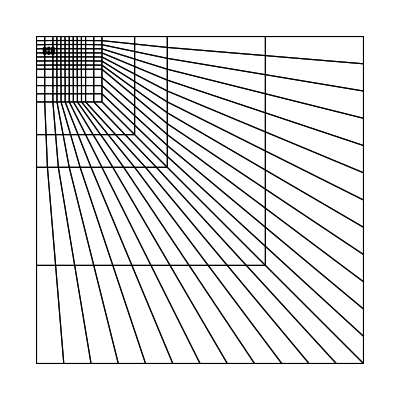

2

{1,3,5,6,8,10,14,18,21,23,27,32,41,49,52,61,69,77,88,93,104,116,130,147,169}

{169,177,197,227,278,308,357,421,512,540,566,591,611,639,663,686,706,716,724,731,739,744,751,755,761,763,767,769,772,773,775,776,777}

{707,717,725,733,740,746,752,756,760,766,771,774,777}

{1,2,4,7,9,11,13,17,22,24,28,33,40,48,53,60,70,78,87,94,103,117,131,148,168}

```mathematica
pack=Developer`ToPackedArray;

(*topol=pack@Transpose@Drop[Transpose@Import["https://www.dropbox.com/s/setx566dvgx3urx/mesh-els-strip-foot-structured4.txt?dl=1","Table"],1];
nnodesAll=Import["https://www.dropbox.com/s/mxelbdwug4yv3lr/mesh-nodes-strip-foot-structured4.txt?dl=1","Table"];*)
topol=pack@Transpose@Drop[Transpose@Import["https://www.dropbox.com/s/vtk5ybrgg69nl79/mesh-els-strip-foot-structured.txt?dl=1","Table"],1];
nnodesAll=Import["https://www.dropbox.com/s/xu5f15vm4k0kmi1/mesh-nodes-strip-foot-structured.txt?dl=1","Table"];

nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=Table[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,8}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Dashing[Tiny]],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
meshVis1=Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{PointSize[Medium],Black,MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Black,Point[nnodes]}}];
nodeVis=Graphics[{PointSize[Medium],Black,{Black,Point[nnodes]}}];
Show[meshVis1];
el=120;
nodeel=Table[nnodes[[topol[[el]][[i]]]],{i,1,Length[topol[[el]]]}]
nodeVis=Graphics[{PointSize[Medium],Black,{Black,Point[nodeel]}}];
Show[meshVis1,nodeVis]
order=2
serendipity=False;

a=500;
b2=50;
x0=0.;xf=a;
y0=0;yf=0;
ndivs=10000;
searchpathinferiorline=Flatten[Table[{x,y},{x,x0,xf,(xf-x0)/ndivs},{y,y0,yf,(yf-y0)/ndivs}],1];
x0=0;xf=0.;
y0=0;yf=a;
searchpathleftline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
x0=0;xf=b2;
y0=a;yf=a;
searchpathupline=Table[{x,y0},{x,x0,xf,(xf-x0)/ndivs}];
x0=a;xf=a;
y0=0;yf=a;
searchpathrigthline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
idsinferior=FindIds[nnodes,searchpathinferiorline]
idsleft=FindIds[nnodes,searchpathleftline]
idssup=FindIds[nnodes,searchpathupline]
idsrigth=FindIds[nnodes,searchpathrigthline]
```

```mathematica
planestress=False;
serendipity=True;
bodyforce=0;
order=2;
eltype=1;


subst2={c->490.,phi->20/180. Pi,young->10^7. (*kPa*),nu->0.48 ,G->young/(2(1+nu)),K->(young)/(3 (1-2nu)),A->3 Tan[phi]/Sqrt[9+12 Tan[phi]^2],
B->3 /Sqrt[9+12 Tan[phi]^2]};


f[x_]:=15 c//.subst2 ;
FEXT=ContributeStraigthLineNewman[nnodes,order,idssup,{0,-1},f];


globalcounter=1;
intrule=IntegrationRule[order,eltype];
npts=Length[intrule]; 
nglobalpts=Length[topol] npts;
epspvec=Table[0,{nglobalpts},{3}];
epspsolitern=Table[0,{nglobalpts},{3}];

solss={};
sol2={{0,0}};
sol3={};
displace=Table[0,{Length[nnodes] 2}];
AppendTo[solss,displace];
epspsolu={};
stresssolu={};
dgammasol={};

lamb=1;
diff=10;
l=0.25;
counterout=1;
tol1=10^-3;
tol2=10^-5;
While[Abs[diff]>tol1 && counterout≤60,

Print["i = ",counterout, " | lamb = ",lamb, " | lambn = ",lambn," | diff = ",diff];
counter=1;
err1=10;
err2=10;

dw=Table[0,{Length[nnodes] 2}];

lambn=lamb;
While[counter≤30&& err2>tol2,

epsppost={};
dgamma={};
stressppost={};
globalcounter=1;
{KT,FINT,FEXTB}=Assemble[allcoords,nnodes,topol,order,eltype,displace];
FEXT+=FEXTB;
imposex=1;
imposey=2;

R=lamb  FEXT-FINT;

{KT,R}=ContributeLineDirichlet[KT,R,idsinferior,{imposey,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsleft,{imposex,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsrigth,{imposex,0}];

dws=LinearSolve[KT,R,Method->"Banded"];
dwb=LinearSolve[KT,FEXT,Method->"Banded"];
a=dwb.dwb;
b=2(dw+dws).dwb;
ccc=(dw+dws).(dw+dws)-l^2;
dlamb=Solve[a x^2 +b x+ccc==0,x][[2,1,2]];
dww=dws+dlamb dwb;
dw+=dww;
lamb+=dlamb;
(*dw=LinearSolve[KT,R];*)
res=Norm[dww];
displace+=dww;
err1=Norm[R]/Norm[lamb  FEXT];
(*If[err1>temp && counter>4,diverge=True];*)
temp=err1;
err2=Norm[dww]/Norm[displace];

Print["Iteration number = " ,counter,"  |R|/|FE| =  ",Norm[R]/Norm[lamb FEXT], "  |Δu|/|u| = ",Norm[dww]/Norm[displace],"  |R| =  ",Norm[R] , " |dw| = ",Norm[dww], " | dlamb = ",dlamb, " | lamb = ",lamb];
counter++;
];
diff=Abs[lamb-lambn];
AppendTo[stresssolu,stressppost];
AppendTo[epspsolu,epsppost];
AppendTo[solss,displace];
id=FindIds[nnodes,{{0,500}}][[1]];
AppendTo[sol2,{-displace[[id 2]]/100, f[x] lamb/c//.subst2}];

AppendTo[sol3,epspvec];
(*Atualiza variável de estado plástica no passo convergido*)
epspsolitern=epspvec;
counterout++;
]
```

i = 1 | lamb = 1 | lambn = 4.17859 | diff = 10

Iteration number = 1  |R|/|FE| =  4.84891  |Δu|/|u| = 1.  |R| =  117105. |dw| = 0.25 | dlamb = -0.793768 | lamb = 0.206232

Iteration number = 2  |R|/|FE| =  1.48174×10^-12  |Δu|/|u| = 1.06359×10^-13  |R| =  3.57851×10^-8 |dw| = 2.65898×10^-14 | dlamb = 1.90726×10^-14 | lamb = 0.206232

i = 2 | lamb = 0.206232 | lambn = 1 | diff = 0.793768

Iteration number = 1  |R|/|FE| =  1.85531×10^-13  |Δu|/|u| = 0.5  |R| =  8.96141×10^-9 |dw| = 0.25 | dlamb = 0.206232 | lamb = 0.412463

Iteration number = 2  |R|/|FE| =  0.0932174  |Δu|/|u| = 0.0123523  |R| =  4489.03 |dw| = 0.00617566 | dlamb = -0.00123654 | lamb = 0.411227

Iteration number = 3  |R|/|FE| =  0.154238  |Δu|/|u| = 0.00287497  |R| =  7424.84 |dw| = 0.00143733 | dlamb = -0.000151626 | lamb = 0.411075

Iteration number = 4  |R|/|FE| =  0.0178126  |Δu|/|u| = 0.000406935  |R| =  857.439 |dw| = 0.000203444 | dlamb = -0.0000185995 | lamb = 0.411057

Iteration number = 5  |R|/|FE| =  0.00328543  |Δu|/|u| = 0.000047534  |R| =  158.149 |dw| = 0.0000237643 | dlamb = -1.74745×10^-6 | lamb = 0.411055

Iteration number = 6  |R|/|FE| =  0.000200145  |Δu|/|u| = 7.06482×10^-7  |R| =  9.63429 |dw| = 3.53201×10^-7 | dlamb = -9.5248×10^-8 | lamb = 0.411055

i = 3 | lamb = 0.411055 | lambn = 0.206232 | diff = 0.204823

Iteration number = 1  |R|/|FE| =  0.00621515  |Δu|/|u| = 0.334354  |R| =  440.357 |dw| = 0.25 | dlamb = 0.193979 | lamb = 0.605034

Iteration number = 2  |R|/|FE| =  0.398767  |Δu|/|u| = 0.0587179  |R| =  27148.5 |dw| = 0.0434892 | dlamb = -0.023665 | lamb = 0.581369

Iteration number = 3  |R|/|FE| =  0.364106  |Δu|/|u| = 0.0135709  |R| =  24556.3 |dw| = 0.0100224 | dlamb = -0.00545179 | lamb = 0.575917

Iteration number = 4  |R|/|FE| =  0.103229  |Δu|/|u| = 0.00286183  |R| =  6949.77 |dw| = 0.00211264 | dlamb = -0.00101448 | lamb = 0.574903

Iteration number = 5  |R|/|FE| =  0.00775936  |Δu|/|u| = 0.00061246  |R| =  522.313 |dw| = 0.0004521 | dlamb = -0.000084657 | lamb = 0.574818

Iteration number = 6  |R|/|FE| =  0.000796662  |Δu|/|u| = 0.0000598789  |R| =  53.6273 |dw| = 0.0000442012 | dlamb = 9.48585×10^-6 | lamb = 0.574827

Iteration number = 7  |R|/|FE| =  0.0000936975  |Δu|/|u| = 0.000010389  |R| =  6.30723 |dw| = 7.66888×10^-6 | dlamb = -1.43631×10^-6 | lamb = 0.574826

Iteration number = 8  |R|/|FE| =  0.0000131597  |Δu|/|u| = 1.22855×10^-6  |R| =  0.88584 |dw| = 9.06886×10^-7 | dlamb = 1.88642×10^-7 | lamb = 0.574826

i = 4 | lamb = 0.574826 | lambn = 0.411055 | diff = 0.163771

Iteration number = 1  |R|/|FE| =  0.0196917  |Δu|/|u| = 0.255256  |R| =  1659.02 |dw| = 0.25 | dlamb = 0.144615 | lamb = 0.719441

Iteration number = 2  |R|/|FE| =  0.299196  |Δu|/|u| = 0.0353485  |R| =  24493.3 |dw| = 0.0343069 | dlamb = -0.0203777 | lamb = 0.699063

Iteration number = 3  |R|/|FE| =  0.126053  |Δu|/|u| = 0.00508593  |R| =  10295.3 |dw| = 0.00493052 | dlamb = -0.00161854 | lamb = 0.697445

Iteration number = 4  |R|/|FE| =  0.033435  |Δu|/|u| = 0.00326679  |R| =  2728.1 |dw| = 0.00316565 | dlamb = -0.000681147 | lamb = 0.696764

Iteration number = 5  |R|/|FE| =  0.0884097  |Δu|/|u| = 0.000663769  |R| =  7214.32 |dw| = 0.000643235 | dlamb = 0.0000572149 | lamb = 0.696821

Iteration number = 6  |R|/|FE| =  0.00817519  |Δu|/|u| = 0.00049864  |R| =  666.988 |dw| = 0.000483174 | dlamb = -0.000120352 | lamb = 0.6967

Iteration number = 7  |R|/|FE| =  0.000599675  |Δu|/|u| = 0.00010902  |R| =  48.9273 |dw| = 0.00010564 | dlamb = 0.0000241075 | lamb = 0.696725

Iteration number = 8  |R|/|FE| =  0.0000309783  |Δu|/|u| = 4.89998×10^-6  |R| =  2.52751 |dw| = 4.74807×10^-6 | dlamb = 6.00074×10^-7 | lamb = 0.696725

i = 5 | lamb = 0.696725 | lambn = 0.574826 | diff = 0.121899

Iteration number = 1  |R|/|FE| =  0.034244  |Δu|/|u| = 0.206442  |R| =  3295.67 |dw| = 0.25 | dlamb = 0.125113 | lamb = 0.821838

Iteration number = 2  |R|/|FE| =  0.335845  |Δu|/|u| = 0.0333668  |R| =  31446.3 |dw| = 0.0400591 | dlamb = -0.0222669 | lamb = 0.799571

Iteration number = 3  |R|/|FE| =  0.302149  |Δu|/|u| = 0.00543465  |R| =  28201.4 |dw| = 0.00651494 | dlamb = -0.00253944 | lamb = 0.797032

Iteration number = 4  |R|/|FE| =  0.0377666  |Δu|/|u| = 0.00119562  |R| =  3523.24 |dw| = 0.00143297 | dlamb = -0.000395439 | lamb = 0.796636

Iteration number = 5  |R|/|FE| =  0.0202619  |Δu|/|u| = 0.000551161  |R| =  1889.98 |dw| = 0.000660531 | dlamb = -0.000105944 | lamb = 0.79653

Iteration number = 6  |R|/|FE| =  0.00548199  |Δu|/|u| = 0.00147413  |R| =  511.184 |dw| = 0.00176639 | dlamb = -0.00025135 | lamb = 0.796279

Iteration number = 7  |R|/|FE| =  0.00958215  |Δu|/|u| = 0.00273782  |R| =  892.996 |dw| = 0.00327969 | dlamb = -0.000463008 | lamb = 0.795816

Iteration number = 8  |R|/|FE| =  0.132075  |Δu|/|u| = 0.00257782  |R| =  12296.4 |dw| = 0.00308659 | dlamb = -0.000785598 | lamb = 0.79503

Iteration number = 9  |R|/|FE| =  0.0171486  |Δu|/|u| = 0.000354081  |R| =  1596.39 |dw| = 0.00042394 | dlamb = -0.000089259 | lamb = 0.794941

Iteration number = 10  |R|/|FE| =  0.00183772  |Δu|/|u| = 0.0000460787  |R| =  171.078 |dw| = 0.0000551702 | dlamb = 0.0000138859 | lamb = 0.794955

Iteration number = 11  |R|/|FE| =  0.000171258  |Δu|/|u| = 0.0000198366  |R| =  15.9431 |dw| = 0.0000237506 | dlamb = 7.16958×10^-6 | lamb = 0.794962

Iteration number = 12  |R|/|FE| =  0.0000161893  |Δu|/|u| = 1.59173×10^-6  |R| =  1.50712 |dw| = 1.90579×10^-6 | dlamb = 5.55759×10^-7 | lamb = 0.794963

i = 6 | lamb = 0.794963 | lambn = 0.696725 | diff = 0.0982374

Iteration number = 1  |R|/|FE| =  0.0420017  |Δu|/|u| = 0.173812  |R| =  4444.06 |dw| = 0.25 | dlamb = 0.108559 | lamb = 0.903521

Iteration number = 2  |R|/|FE| =  0.260666  |Δu|/|u| = 0.03349  |R| =  26765. |dw| = 0.0477163 | dlamb = -0.0267052 | lamb = 0.876816

Iteration number = 3  |R|/|FE| =  0.254944  |Δu|/|u| = 0.00555641  |R| =  26081. |dw| = 0.00790276 | dlamb = -0.00323019 | lamb = 0.873586

Iteration number = 4  |R|/|FE| =  0.0519447  |Δu|/|u| = 0.000594591  |R| =  5312.12 |dw| = 0.000845522 | dlamb = -0.000308081 | lamb = 0.873278

Iteration number = 5  |R|/|FE| =  0.00693358  |Δu|/|u| = 0.0000682102  |R| =  709.039 |dw| = 0.000096995 | dlamb = -0.0000273294 | lamb = 0.87325

Iteration number = 6  |R|/|FE| =  0.00105792  |Δu|/|u| = 0.0000129849  |R| =  108.185 |dw| = 0.0000184646 | dlamb = 3.3872×10^-6 | lamb = 0.873254

Iteration number = 7  |R|/|FE| =  0.0000236592  |Δu|/|u| = 2.61281×10^-6  |R| =  2.41944 |dw| = 3.71543×10^-6 | dlamb = 4.57339×10^-7 | lamb = 0.873254

i = 7 | lamb = 0.873254 | lambn = 0.794963 | diff = 0.0782917

Iteration number = 1  |R|/|FE| =  0.0250183  |Δu|/|u| = 0.150564  |R| =  2820.7 |dw| = 0.25 | dlamb = 0.0895242 | lamb = 0.962778

Iteration number = 2  |R|/|FE| =  0.270049  |Δu|/|u| = 0.0324339  |R| =  29516.8 |dw| = 0.0533142 | dlamb = -0.02941 | lamb = 0.933368

Iteration number = 3  |R|/|FE| =  0.144762  |Δu|/|u| = 0.00521425  |R| =  15780.4 |dw| = 0.00855867 | dlamb = -0.00250036 | lamb = 0.930868

Iteration number = 4  |R|/|FE| =  0.0237047  |Δu|/|u| = 0.00178828  |R| =  2583.12 |dw| = 0.00293464 | dlamb = -0.000327794 | lamb = 0.93054

Iteration number = 5  |R|/|FE| =  0.0166758  |Δu|/|u| = 0.00236705  |R| =  1817.76 |dw| = 0.00388505 | dlamb = 0.00029782 | lamb = 0.930838

Iteration number = 6  |R|/|FE| =  0.0232426  |Δu|/|u| = 0.00185217  |R| =  2532.66 |dw| = 0.00303939 | dlamb = -0.000331871 | lamb = 0.930506

Iteration number = 7  |R|/|FE| =  0.00884153  |Δu|/|u| = 0.000274835  |R| =  963.39 |dw| = 0.000450992 | dlamb = -0.0000400053 | lamb = 0.930466

Iteration number = 8  |R|/|FE| =  0.00181973  |Δu|/|u| = 0.000298769  |R| =  198.266 |dw| = 0.000490252 | dlamb = -0.0000721881 | lamb = 0.930394

Iteration number = 9  |R|/|FE| =  0.000966991  |Δu|/|u| = 0.000100006  |R| =  105.355 |dw| = 0.000164099 | dlamb = -0.0000215685 | lamb = 0.930372

Iteration number = 10  |R|/|FE| =  0.000473682  |Δu|/|u| = 0.0000661302  |R| =  51.6071 |dw| = 0.000108512 | dlamb = -0.0000164911 | lamb = 0.930356

Iteration number = 11  |R|/|FE| =  0.00018947  |Δu|/|u| = 0.0000176723  |R| =  20.6425 |dw| = 0.0000289982 | dlamb = -3.80643×10^-6 | lamb = 0.930352

Iteration number = 12  |R|/|FE| =  0.0000691845  |Δu|/|u| = 9.60975×10^-6  |R| =  7.53753 |dw| = 0.0000157685 | dlamb = -2.40087×10^-6 | lamb = 0.93035

i = 8 | lamb = 0.93035 | lambn = 0.873254 | diff = 0.0570955

Iteration number = 1  |R|/|FE| =  0.028751  |Δu|/|u| = 0.133146  |R| =  3383.42 |dw| = 0.25 | dlamb = 0.0745634 | lamb = 1.00491

Iteration number = 2  |R|/|FE| =  0.292331  |Δu|/|u| = 0.0320009  |R| =  33238.2 |dw| = 0.0594276 | dlamb = -0.0339825 | lamb = 0.970931

Iteration number = 3  |R|/|FE| =  0.151146  |Δu|/|u| = 0.00489814  |R| =  17134.4 |dw| = 0.00908203 | dlamb = -0.00287925 | lamb = 0.968051

Iteration number = 4  |R|/|FE| =  0.0421393  |Δu|/|u| = 0.00264747  |R| =  4773.54 |dw| = 0.0049071 | dlamb = -0.000711295 | lamb = 0.96734

Iteration number = 5  |R|/|FE| =  0.0175397  |Δu|/|u| = 0.000715703  |R| =  1986.52 |dw| = 0.00132644 | dlamb = -0.000182139 | lamb = 0.967158

Iteration number = 6  |R|/|FE| =  0.00824385  |Δu|/|u| = 0.000676052  |R| =  933.881 |dw| = 0.00125302 | dlamb = 0.000200306 | lamb = 0.967358

Iteration number = 7  |R|/|FE| =  0.00599742  |Δu|/|u| = 0.000319257  |R| =  679.462 |dw| = 0.000591734 | dlamb = 0.0000869054 | lamb = 0.967445

Iteration number = 8  |R|/|FE| =  0.00209033  |Δu|/|u| = 0.000149015  |R| =  236.824 |dw| = 0.000276195 | dlamb = 0.0000226273 | lamb = 0.967468

Iteration number = 9  |R|/|FE| =  0.000783024  |Δu|/|u| = 0.000111518  |R| =  88.7156 |dw| = 0.000206698 | dlamb = 0.0000316371 | lamb = 0.967499

Iteration number = 10  |R|/|FE| =  0.000332524  |Δu|/|u| = 0.0000281959  |R| =  37.6746 |dw| = 0.0000522608 | dlamb = 3.07038×10^-6 | lamb = 0.967503

Iteration number = 11  |R|/|FE| =  0.00019517  |Δu|/|u| = 0.0000280188  |R| =  22.1128 |dw| = 0.0000519328 | dlamb = 7.92239×10^-6 | lamb = 0.96751

Iteration number = 12  |R|/|FE| =  0.000113676  |Δu|/|u| = 9.75013×10^-6  |R| =  12.8795 |dw| = 0.0000180719 | dlamb = 2.26279×10^-6 | lamb = 0.967513

i = 9 | lamb = 0.967513 | lambn = 0.93035 | diff = 0.0371629

Iteration number = 1  |R|/|FE| =  0.0329177  |Δu|/|u| = 0.119903  |R| =  3950.29 |dw| = 0.25 | dlamb = 0.0572554 | lamb = 1.02477

Iteration number = 2  |R|/|FE| =  0.194081  |Δu|/|u| = 0.0321881  |R| =  22473.7 |dw| = 0.0662482 | dlamb = -0.035945 | lamb = 0.988823

Iteration number = 3  |R|/|FE| =  0.0918791  |Δu|/|u| = 0.00470921  |R| =  10611.9 |dw| = 0.00967629 | dlamb = -0.00253926 | lamb = 0.986284

Iteration number = 4  |R|/|FE| =  0.0346466  |Δu|/|u| = 0.00340383  |R| =  3996.67 |dw| = 0.00698837 | dlamb = -0.00122245 | lamb = 0.985061

Iteration number = 5  |R|/|FE| =  0.0692776  |Δu|/|u| = 0.00181266  |R| =  7987.2 |dw| = 0.00372036 | dlamb = -0.000533554 | lamb = 0.984528

Iteration number = 6  |R|/|FE| =  0.0390117  |Δu|/|u| = 0.000546471  |R| =  4496.78 |dw| = 0.00112147 | dlamb = -0.000217558 | lamb = 0.98431

Iteration number = 7  |R|/|FE| =  0.0097835  |Δu|/|u| = 0.000621092  |R| =  1127.51 |dw| = 0.00127446 | dlamb = -0.000178441 | lamb = 0.984132

Iteration number = 8  |R|/|FE| =  0.00884524  |Δu|/|u| = 0.000397349  |R| =  1019.55 |dw| = 0.000815403 | dlamb = 0.000161078 | lamb = 0.984293

Iteration number = 9  |R|/|FE| =  0.00425147  |Δu|/|u| = 0.000328093  |R| =  490.114 |dw| = 0.000673321 | dlamb = 0.000133278 | lamb = 0.984426

Iteration number = 10  |R|/|FE| =  0.00145474  |Δu|/|u| = 0.000192829  |R| =  167.716 |dw| = 0.000395743 | dlamb = 0.0000757763 | lamb = 0.984502

Iteration number = 11  |R|/|FE| =  0.000610645  |Δu|/|u| = 0.0000482943  |R| =  70.4023 |dw| = 0.0000991148 | dlamb = 0.0000153616 | lamb = 0.984517

Iteration number = 12  |R|/|FE| =  0.000404939  |Δu|/|u| = 0.0000576437  |R| =  46.6871 |dw| = 0.000118304 | dlamb = 0.0000215703 | lamb = 0.984539

Iteration number = 13  |R|/|FE| =  0.000294172  |Δu|/|u| = 0.0000316707  |R| =  33.9167 |dw| = 0.000064999 | dlamb = 0.0000112913 | lamb = 0.98455

Iteration number = 14  |R|/|FE| =  0.000250416  |Δu|/|u| = 0.0000345623  |R| =  28.8722 |dw| = 0.0000709341 | dlamb = 0.000012501 | lamb = 0.984563

Iteration number = 15  |R|/|FE| =  0.000207201  |Δu|/|u| = 0.000025994  |R| =  23.8899 |dw| = 0.0000533491 | dlamb = 9.1807×10^-6 | lamb = 0.984572

Iteration number = 16  |R|/|FE| =  0.000181489  |Δu|/|u| = 0.0000250119  |R| =  20.9255 |dw| = 0.0000513336 | dlamb = 8.799×10^-6 | lamb = 0.984581

Iteration number = 17  |R|/|FE| =  0.00015758  |Δu|/|u| = 0.000021216  |R| =  18.169 |dw| = 0.0000435433 | dlamb = 7.34418×10^-6 | lamb = 0.984588

Iteration number = 18  |R|/|FE| =  0.000140607  |Δu|/|u| = 0.0000197388  |R| =  16.2121 |dw| = 0.0000405117 | dlamb = 6.78532×10^-6 | lamb = 0.984595

Iteration number = 19  |R|/|FE| =  0.000125557  |Δu|/|u| = 0.0000176323  |R| =  14.4769 |dw| = 0.0000361884 | dlamb = 5.99226×10^-6 | lamb = 0.984601

Iteration number = 20  |R|/|FE| =  0.000113732  |Δu|/|u| = 0.0000163336  |R| =  13.1135 |dw| = 0.0000335231 | dlamb = 5.51093×10^-6 | lamb = 0.984606

Iteration number = 21  |R|/|FE| =  0.000103384  |Δu|/|u| = 0.0000149555  |R| =  11.9205 |dw| = 0.0000306948 | dlamb = 5.00219×10^-6 | lamb = 0.984611

Iteration number = 22  |R|/|FE| =  0.0000947675  |Δu|/|u| = 0.0000139092  |R| =  10.927 |dw| = 0.0000285474 | dlamb = 4.62106×10^-6 | lamb = 0.984616

Iteration number = 23  |R|/|FE| =  0.0000872091  |Δu|/|u| = 0.0000129109  |R| =  10.0555 |dw| = 0.0000264985 | dlamb = 4.25919×10^-6 | lamb = 0.98462

Iteration number = 24  |R|/|FE| =  0.0000806948  |Δu|/|u| = 0.0000120763  |R| =  9.30444 |dw| = 0.0000247856 | dlamb = 3.95985×10^-6 | lamb = 0.984624

Iteration number = 25  |R|/|FE| =  0.0000749318  |Δu|/|u| = 0.0000113076  |R| =  8.63998 |dw| = 0.0000232079 | dlamb = 3.68572×10^-6 | lamb = 0.984628

Iteration number = 26  |R|/|FE| =  0.0000698547  |Δu|/|u| = 0.0000106343  |R| =  8.05459 |dw| = 0.0000218261 | dlamb = 3.44766×10^-6 | lamb = 0.984631

Iteration number = 27  |R|/|FE| =  0.000065318  |Δu|/|u| = 0.0000100192  |R| =  7.53151 |dw| = 0.0000205637 | dlamb = 3.23147×10^-6 | lamb = 0.984634

Iteration number = 28  |R|/|FE| =  0.0000612598  |Δu|/|u| = 9.46704×10^-6  |R| =  7.0636 |dw| = 0.0000194305 | dlamb = 3.0388×10^-6 | lamb = 0.984638

i = 10 | lamb = 0.984638 | lambn = 0.967513 | diff = 0.0171248

Iteration number = 1  |R|/|FE| =  0.0376157  |Δu|/|u| = 0.109485  |R| =  4558.07 |dw| = 0.25 | dlamb = 0.0501173 | lamb = 1.03475

Iteration number = 2  |R|/|FE| =  0.195904  |Δu|/|u| = 0.0349649  |R| =  22819.7 |dw| = 0.078684 | dlamb = -0.0400536 | lamb = 0.994701

Iteration number = 3  |R|/|FE| =  0.100187  |Δu|/|u| = 0.0045248  |R| =  11643.8 |dw| = 0.0101667 | dlamb = -0.00224992 | lamb = 0.992451

Iteration number = 4  |R|/|FE| =  0.0441427  |Δu|/|u| = 0.00369374  |R| =  5124.38 |dw| = 0.00829206 | dlamb = -0.00114463 | lamb = 0.991307

Iteration number = 5  |R|/|FE| =  0.0915981  |Δu|/|u| = 0.00216978  |R| =  10625.2 |dw| = 0.00486833 | dlamb = -0.000758279 | lamb = 0.990548

Iteration number = 6  |R|/|FE| =  0.0579672  |Δu|/|u| = 0.00137273  |R| =  6720.09 |dw| = 0.00307881 | dlamb = -0.000586117 | lamb = 0.989962

Iteration number = 7  |R|/|FE| =  0.0117049  |Δu|/|u| = 0.000704143  |R| =  1356.61 |dw| = 0.00157899 | dlamb = -0.000246646 | lamb = 0.989716

Iteration number = 8  |R|/|FE| =  0.0130933  |Δu|/|u| = 0.000319659  |R| =  1517.57 |dw| = 0.000716804 | dlamb = 0.0000274985 | lamb = 0.989743

Iteration number = 9  |R|/|FE| =  0.00650079  |Δu|/|u| = 0.000721154  |R| =  753.706 |dw| = 0.00161745 | dlamb = 0.000317156 | lamb = 0.99006

Iteration number = 10  |R|/|FE| =  0.00299719  |Δu|/|u| = 0.000181979  |R| =  347.526 |dw| = 0.000408172 | dlamb = 0.0000847752 | lamb = 0.990145

Iteration number = 11  |R|/|FE| =  0.00210378  |Δu|/|u| = 0.000248873  |R| =  243.956 |dw| = 0.000558246 | dlamb = 0.0000844379 | lamb = 0.990229

Iteration number = 12  |R|/|FE| =  0.000486826  |Δu|/|u| = 0.000141295  |R| =  56.4498 |dw| = 0.000316928 | dlamb = -0.0000501145 | lamb = 0.990179

Iteration number = 13  |R|/|FE| =  0.000224773  |Δu|/|u| = 0.0000539767  |R| =  26.0639 |dw| = 0.000121072 | dlamb = 0.0000142576 | lamb = 0.990194

Iteration number = 14  |R|/|FE| =  0.000115278  |Δu|/|u| = 0.0000362639  |R| =  13.3671 |dw| = 0.0000813409 | dlamb = -0.0000129936 | lamb = 0.990181

Iteration number = 15  |R|/|FE| =  0.0000505172  |Δu|/|u| = 0.0000135406  |R| =  5.85773 |dw| = 0.0000303721 | dlamb = 4.14046×10^-6 | lamb = 0.990185

Iteration number = 16  |R|/|FE| =  0.0000233104  |Δu|/|u| = 6.68016×10^-6  |R| =  2.70296 |dw| = 0.0000149838 | dlamb = -2.14355×10^-6 | lamb = 0.990183

i = 11 | lamb = 0.990183 | lambn = 0.984638 | diff = 0.00554511

Iteration number = 1  |R|/|FE| =  0.0451216  |Δu|/|u| = 0.100899  |R| =  5476.68 |dw| = 0.25 | dlamb = 0.0462924 | lamb = 1.03647

Iteration number = 2  |R|/|FE| =  0.215503  |Δu|/|u| = 0.0330809  |R| =  25179.9 |dw| = 0.080941 | dlamb = -0.0387164 | lamb = 0.997759

Iteration number = 3  |R|/|FE| =  0.0767177  |Δu|/|u| = 0.00454883  |R| =  8945.38 |dw| = 0.0111136 | dlamb = -0.00205822 | lamb = 0.9957

Iteration number = 4  |R|/|FE| =  0.0297918  |Δu|/|u| = 0.00400511  |R| =  3469.01 |dw| = 0.00977617 | dlamb = -0.00135903 | lamb = 0.994341

Iteration number = 5  |R|/|FE| =  0.0283073  |Δu|/|u| = 0.00361266  |R| =  3291.49 |dw| = 0.00880943 | dlamb = -0.00140787 | lamb = 0.992933

Iteration number = 6  |R|/|FE| =  0.0294689  |Δu|/|u| = 0.0016294  |R| =  3424.47 |dw| = 0.00397141 | dlamb = -0.000605061 | lamb = 0.992328

Iteration number = 7  |R|/|FE| =  0.0125803  |Δu|/|u| = 0.00106863  |R| =  1462.6 |dw| = 0.00260544 | dlamb = 0.000467562 | lamb = 0.992796

Iteration number = 8  |R|/|FE| =  0.00665249  |Δu|/|u| = 0.000505829  |R| =  773.606 |dw| = 0.00123346 | dlamb = 0.000232106 | lamb = 0.993028

Iteration number = 9  |R|/|FE| =  0.00318915  |Δu|/|u| = 0.000400717  |R| =  370.929 |dw| = 0.00097726 | dlamb = 0.000184398 | lamb = 0.993213

Iteration number = 10  |R|/|FE| =  0.00132225  |Δu|/|u| = 0.000358398  |R| =  153.813 |dw| = 0.000874143 | dlamb = 0.000146605 | lamb = 0.993359

Iteration number = 11  |R|/|FE| =  0.000444582  |Δu|/|u| = 0.0000494507  |R| =  51.718 |dw| = 0.000120613 | dlamb = 0.0000222677 | lamb = 0.993381

Iteration number = 12  |R|/|FE| =  0.000354508  |Δu|/|u| = 0.000117328  |R| =  41.2416 |dw| = 0.000286179 | dlamb = 0.0000452658 | lamb = 0.993427

Iteration number = 13  |R|/|FE| =  0.000141847  |Δu|/|u| = 0.0000273957  |R| =  16.5017 |dw| = 0.0000668215 | dlamb = -7.48194×10^-6 | lamb = 0.993419

Iteration number = 14  |R|/|FE| =  0.000156591  |Δu|/|u| = 0.0000537031  |R| =  18.2172 |dw| = 0.000130991 | dlamb = 0.0000199545 | lamb = 0.993439

Iteration number = 15  |R|/|FE| =  0.0000918383  |Δu|/|u| = 0.0000273316  |R| =  10.684 |dw| = 0.0000666656 | dlamb = -9.19132×10^-6 | lamb = 0.99343

Iteration number = 16  |R|/|FE| =  0.0000884531  |Δu|/|u| = 0.0000300157  |R| =  10.2903 |dw| = 0.0000732133 | dlamb = 0.0000108845 | lamb = 0.993441

Iteration number = 17  |R|/|FE| =  0.0000627392  |Δu|/|u| = 0.0000201099  |R| =  7.29881 |dw| = 0.0000490512 | dlamb = -7.00396×10^-6 | lamb = 0.993434

Iteration number = 18  |R|/|FE| =  0.0000546048  |Δu|/|u| = 0.0000182878  |R| =  6.35253 |dw| = 0.0000446069 | dlamb = 6.54918×10^-6 | lamb = 0.99344

Iteration number = 19  |R|/|FE| =  0.0000418099  |Δu|/|u| = 0.0000136693  |R| =  4.86399 |dw| = 0.0000333416 | dlamb = -4.81402×10^-6 | lamb = 0.993436

Iteration number = 20  |R|/|FE| =  0.0000347842  |Δu|/|u| = 0.0000115641  |R| =  4.04667 |dw| = 0.0000282067 | dlamb = 4.11789×10^-6 | lamb = 0.99344

Iteration number = 21  |R|/|FE| =  0.0000274579  |Δu|/|u| = 9.03733×10^-6  |R| =  3.19434 |dw| = 0.0000220434 | dlamb = -3.19596×10^-6 | lamb = 0.993436

i = 12 | lamb = 0.993436 | lambn = 0.990183 | diff = 0.00325384

Iteration number = 1  |R|/|FE| =  0.0458744  |Δu|/|u| = 0.09336  |R| =  5580.73 |dw| = 0.25 | dlamb = 0.0453994 | lamb = 1.03884

Iteration number = 2  |R|/|FE| =  0.436929  |Δu|/|u| = 0.0296414  |R| =  51224.3 |dw| = 0.0786101 | dlamb = -0.0377034 | lamb = 1.00113

Iteration number = 3  |R|/|FE| =  0.112111  |Δu|/|u| = 0.00597448  |R| =  13110. |dw| = 0.0158171 | dlamb = -0.00255743 | lamb = 0.998575

Iteration number = 4  |R|/|FE| =  0.0425925  |Δu|/|u| = 0.00570958  |R| =  4970.95 |dw| = 0.0150949 | dlamb = -0.00194893 | lamb = 0.996626

Iteration number = 5  |R|/|FE| =  0.0839865  |Δu|/|u| = 0.00354686  |R| =  9786.41 |dw| = 0.00936728 | dlamb = -0.00158775 | lamb = 0.995038

Iteration number = 6  |R|/|FE| =  0.024003  |Δu|/|u| = 0.00229562  |R| =  2794.49 |dw| = 0.00605873 | dlamb = -0.000859591 | lamb = 0.994179

Iteration number = 7  |R|/|FE| =  0.0167674  |Δu|/|u| = 0.00174031  |R| =  1953.62 |dw| = 0.00459562 | dlamb = 0.000768303 | lamb = 0.994947

Iteration number = 8  |R|/|FE| =  0.00472053  |Δu|/|u| = 0.00025403  |R| =  550.085 |dw| = 0.000670863 | dlamb = 0.000149018 | lamb = 0.995096

Iteration number = 9  |R|/|FE| =  0.0034453  |Δu|/|u| = 0.000620932  |R| =  401.595 |dw| = 0.00164011 | dlamb = 0.00028018 | lamb = 0.995376

Iteration number = 10  |R|/|FE| =  0.00116468  |Δu|/|u| = 0.000151885  |R| =  135.755 |dw| = 0.000401171 | dlamb = -0.0000324841 | lamb = 0.995344

Iteration number = 11  |R|/|FE| =  0.00078572  |Δu|/|u| = 0.000284883  |R| =  91.5936 |dw| = 0.000752517 | dlamb = 0.000115108 | lamb = 0.995459

Iteration number = 12  |R|/|FE| =  0.000422607  |Δu|/|u| = 0.000133911  |R| =  49.262 |dw| = 0.000353714 | dlamb = -0.0000485876 | lamb = 0.99541

Iteration number = 13  |R|/|FE| =  0.000354531  |Δu|/|u| = 0.000131802  |R| =  41.3288 |dw| = 0.000348155 | dlamb = 0.0000508439 | lamb = 0.995461

Iteration number = 14  |R|/|FE| =  0.000248977  |Δu|/|u| = 0.0000887601  |R| =  29.023 |dw| = 0.000234454 | dlamb = -0.0000335162 | lamb = 0.995428

Iteration number = 15  |R|/|FE| =  0.000191845  |Δu|/|u| = 0.0000702322  |R| =  22.3638 |dw| = 0.000185517 | dlamb = 0.0000267517 | lamb = 0.995454

Iteration number = 16  |R|/|FE| =  0.000143496  |Δu|/|u| = 0.0000520045  |R| =  16.7273 |dw| = 0.000137367 | dlamb = -0.0000197408 | lamb = 0.995435

Iteration number = 17  |R|/|FE| =  0.000108433  |Δu|/|u| = 0.0000395185  |R| =  12.6402 |dw| = 0.000104387 | dlamb = 0.0000150239 | lamb = 0.99545

Iteration number = 18  |R|/|FE| =  0.0000818035  |Δu|/|u| = 0.0000297292  |R| =  9.53587 |dw| = 0.0000785284 | dlamb = -0.0000112925 | lamb = 0.995438

Iteration number = 19  |R|/|FE| =  0.0000616979  |Δu|/|u| = 0.0000224664  |R| =  7.19221 |dw| = 0.0000593445 | dlamb = 8.53877×10^-6 | lamb = 0.995447

Iteration number = 20  |R|/|FE| =  0.0000465726  |Δu|/|u| = 0.0000169368  |R| =  5.42901 |dw| = 0.0000447378 | dlamb = -6.43417×10^-6 | lamb = 0.99544

Iteration number = 21  |R|/|FE| =  0.0000351332  |Δu|/|u| = 0.0000127897  |R| =  4.09553 |dw| = 0.0000337837 | dlamb = 4.86048×10^-6 | lamb = 0.995445

Iteration number = 22  |R|/|FE| =  0.0000265169  |Δu|/|u| = 9.64589×10^-6  |R| =  3.0911 |dw| = 0.0000254792 | dlamb = -3.66469×10^-6 | lamb = 0.995442

i = 13 | lamb = 0.995442 | lambn = 0.993436 | diff = 0.00200517

Iteration number = 1  |R|/|FE| =  0.0516578  |Δu|/|u| = 0.0867163  |R| =  6298.09 |dw| = 0.25 | dlamb = 0.045674 | lamb = 1.04112

Iteration number = 2  |R|/|FE| =  0.508768  |Δu|/|u| = 0.0275034  |R| =  59783.8 |dw| = 0.078688 | dlamb = -0.0376806 | lamb = 1.00344

Iteration number = 3  |R|/|FE| =  0.170516  |Δu|/|u| = 0.00522811  |R| =  19989.4 |dw| = 0.0149371 | dlamb = -0.00237135 | lamb = 1.00106

Iteration number = 4  |R|/|FE| =  0.0386794  |Δu|/|u| = 0.00277841  |R| =  4530.42 |dw| = 0.00793301 | dlamb = -0.000869031 | lamb = 1.00019

Iteration number = 5  |R|/|FE| =  0.0219147  |Δu|/|u| = 0.00342116  |R| =  2563.36 |dw| = 0.00976113 | dlamb = -0.00134616 | lamb = 0.998848

Iteration number = 6  |R|/|FE| =  0.0384998  |Δu|/|u| = 0.00471128  |R| =  4493.77 |dw| = 0.0134249 | dlamb = -0.00211709 | lamb = 0.996731

Iteration number = 7  |R|/|FE| =  0.0778828  |Δu|/|u| = 0.00249726  |R| =  9080.6 |dw| = 0.00711061 | dlamb = -0.00109968 | lamb = 0.995632

Iteration number = 8  |R|/|FE| =  0.0159004  |Δu|/|u| = 0.0011614  |R| =  1854.85 |dw| = 0.00330808 | dlamb = 0.000521017 | lamb = 0.996153

Iteration number = 9  |R|/|FE| =  0.00891269  |Δu|/|u| = 0.00123916  |R| =  1040.3 |dw| = 0.00353088 | dlamb = 0.00056997 | lamb = 0.996723

Iteration number = 10  |R|/|FE| =  0.0043282  |Δu|/|u| = 0.000528936  |R| =  505.111 |dw| = 0.00150696 | dlamb = -0.000157796 | lamb = 0.996565

Iteration number = 11  |R|/|FE| =  0.00306712  |Δu|/|u| = 0.00113168  |R| =  358.114 |dw| = 0.00322526 | dlamb = 0.00048358 | lamb = 0.997048

Iteration number = 12  |R|/|FE| =  0.00152534  |Δu|/|u| = 0.000304306  |R| =  178.081 |dw| = 0.000867197 | dlamb = -0.000089889 | lamb = 0.996959

Iteration number = 13  |R|/|FE| =  0.00129087  |Δu|/|u| = 0.000506832  |R| =  150.739 |dw| = 0.00144455 | dlamb = 0.000210754 | lamb = 0.997169

Iteration number = 14  |R|/|FE| =  0.000883171  |Δu|/|u| = 0.000287528  |R| =  103.12 |dw| = 0.000819439 | dlamb = -0.000103209 | lamb = 0.997066

Iteration number = 15  |R|/|FE| =  0.000744594  |Δu|/|u| = 0.000272678  |R| =  86.9492 |dw| = 0.000777172 | dlamb = 0.000109206 | lamb = 0.997175

Iteration number = 16  |R|/|FE| =  0.00059134  |Δu|/|u| = 0.000207669  |R| =  69.0476 |dw| = 0.000591855 | dlamb = -0.0000786915 | lamb = 0.997097

Iteration number = 17  |R|/|FE| =  0.000510811  |Δu|/|u| = 0.00018591  |R| =  59.649 |dw| = 0.000529868 | dlamb = 0.0000728482 | lamb = 0.997169

Iteration number = 18  |R|/|FE| =  0.000423779  |Δu|/|u| = 0.00015188  |R| =  49.4831 |dw| = 0.00043286 | dlamb = -0.0000583972 | lamb = 0.997111

Iteration number = 19  |R|/|FE| =  0.000360769  |Δu|/|u| = 0.000130719  |R| =  42.1279 |dw| = 0.000372565 | dlamb = 0.0000508311 | lamb = 0.997162

Iteration number = 20  |R|/|FE| =  0.000302985  |Δu|/|u| = 0.000109217  |R| =  35.3788 |dw| = 0.000311273 | dlamb = -0.0000421823 | lamb = 0.99712

Iteration number = 21  |R|/|FE| =  0.000256694  |Δu|/|u| = 0.0000928778  |R| =  29.9746 |dw| = 0.000264712 | dlamb = 0.0000360232 | lamb = 0.997156

Iteration number = 22  |R|/|FE| =  0.000216435  |Δu|/|u| = 0.000078167  |R| =  25.2727 |dw| = 0.00022278 | dlamb = -0.0000302348 | lamb = 0.997126

Iteration number = 23  |R|/|FE| =  0.00018309  |Δu|/|u| = 0.00006622  |R| =  21.3796 |dw| = 0.000188733 | dlamb = 0.0000256605 | lamb = 0.997151

Iteration number = 24  |R|/|FE| =  0.000154591  |Δu|/|u| = 0.0000558708  |R| =  18.0514 |dw| = 0.000159235 | dlamb = -0.0000216223 | lamb = 0.99713

Iteration number = 25  |R|/|FE| =  0.000130712  |Δu|/|u| = 0.0000472715  |R| =  15.2633 |dw| = 0.000134728 | dlamb = 0.0000183115 | lamb = 0.997148

Iteration number = 26  |R|/|FE| =  0.000110426  |Δu|/|u| = 0.0000399206  |R| =  12.8943 |dw| = 0.000113776 | dlamb = -0.0000154529 | lamb = 0.997132

Iteration number = 27  |R|/|FE| =  0.0000933545  |Δu|/|u| = 0.0000337605  |R| =  10.901 |dw| = 0.0000962203 | dlamb = 0.0000130756 | lamb = 0.997145

Iteration number = 28  |R|/|FE| =  0.0000788847  |Δu|/|u| = 0.0000285217  |R| =  9.21129 |dw| = 0.0000812886 | dlamb = -0.0000110417 | lamb = 0.997134

Iteration number = 29  |R|/|FE| =  0.000066685  |Δu|/|u| = 0.0000241156  |R| =  7.78682 |dw| = 0.0000687316 | dlamb = 9.33934×10^-6 | lamb = 0.997144

Iteration number = 30  |R|/|FE| =  0.0000563554  |Δu|/|u| = 0.0000203773  |R| =  6.58058 |dw| = 0.0000580767 | dlamb = -7.88922×10^-6 | lamb = 0.997136

i = 14 | lamb = 0.997136 | lambn = 0.995442 | diff = 0.00169427

Iteration number = 1  |R|/|FE| =  0.0553178  |Δu|/|u| = 0.0808208  |R| =  6755.34 |dw| = 0.25 | dlamb = 0.045681 | lamb = 1.04282

Iteration number = 2  |R|/|FE| =  0.645069  |Δu|/|u| = 0.0252262  |R| =  75953.2 |dw| = 0.0775753 | dlamb = -0.0373541 | lamb = 1.00546

Iteration number = 3  |R|/|FE| =  0.105949  |Δu|/|u| = 0.00524298  |R| =  12443.6 |dw| = 0.0161029 | dlamb = -0.00251782 | lamb = 1.00294

Iteration number = 4  |R|/|FE| =  0.0388114  |Δu|/|u| = 0.00268612  |R| =  4554.41 |dw| = 0.00824539 | dlamb = -0.000872191 | lamb = 1.00207

Iteration number = 5  |R|/|FE| =  0.0217594  |Δu|/|u| = 0.0027617  |R| =  2550.52 |dw| = 0.00847278 | dlamb = -0.00113053 | lamb = 1.00094

Iteration number = 6  |R|/|FE| =  0.0345352  |Δu|/|u| = 0.00562977  |R| =  4037.59 |dw| = 0.0172478 | dlamb = -0.00258357 | lamb = 0.998359

Iteration number = 7  |R|/|FE| =  0.0839506  |Δu|/|u| = 0.00346335  |R| =  9798.1 |dw| = 0.0105992 | dlamb = -0.00170587 | lamb = 0.996653

Iteration number = 8  |R|/|FE| =  0.0328942  |Δu|/|u| = 0.000938695  |R| =  3840.06 |dw| = 0.00287305 | dlamb = 0.000230272 | lamb = 0.996883

Iteration number = 9  |R|/|FE| =  0.0107663  |Δu|/|u| = 0.00190107  |R| =  1257.85 |dw| = 0.00582186 | dlamb = 0.000795942 | lamb = 0.997679

$Aborted

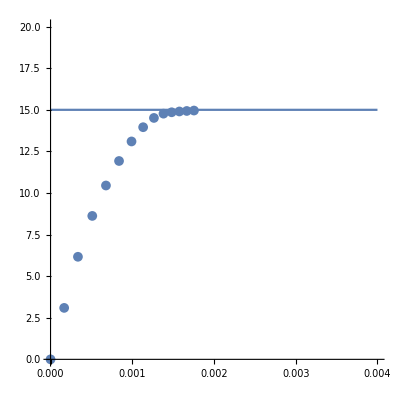

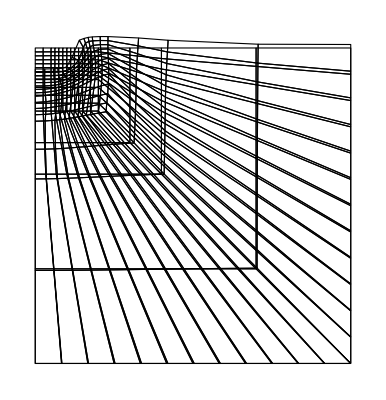

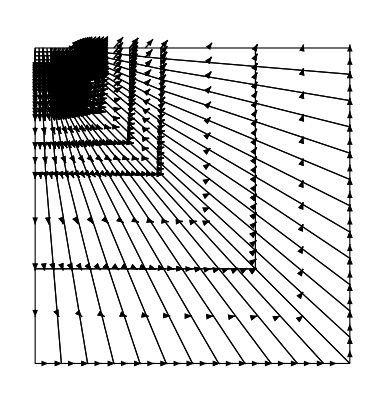

```mathematica
solu=13;
Show[ListPlot[sol2,AspectRatio->1,PlotMarkers->{Automatic, 10}],Plot[15.,{x,0,0.004}],PlotRange->{{0,0.004},{0,20}}]
sol=solss[[solu]];
scale=200;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=Table[{deformed[[i]],deformed[[i+1]]},{i,1,Length[deformed],2}];
g=Show[meshVis1,Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}]]


{vecs2,vecs3}=ComputeSolNoInterpolation[topol,nnodes,order,sol,eltype,scale];
arrows=Table[Graphics[{Arrowheads[.02],Arrow[{vecs2[[el]][[i]][[1]],vecs2[[el]][[i]][[2]]}]}],{el,1,Length[vecs2]},{i,1,Length[vecs2[[el]]]}];
sh=Show[meshVis1,arrows,PlotRange->All]

(*teste1=Table[{dgammasol[[solu]][[i]][[1]],dgammasol[[solu]][[i]][[2]],dgammasol[[solu]][[i]][[3]]},{i,1,Length[dgammasol[[solu]]]}];
Show[ListContourPlot[teste1,PlotLegends->{Placed[Automatic,{Right,Center}]}],PlotRange->All,AspectRatio->Automatic,Frame->False]
ListContourPlot[vecs3]*)
(*show[{{0,340},{160,515}},sh]*)

(*tab=Table[{epspsolu[[solu]][[i]][[1]],epspsolu[[solu]][[i]][[2]],Norm[epspsolu[[solu]][[i]][[3]]]},{i,1,Length[epspsolu[[solu]]]}];
ListContourPlot[tab]*)


(*tab=Table[{stresssolu[[solu]][[i]][[1]],stresssolu[[solu]][[i]][[2]],stresssolu[[solu]][[i]][[3]][[3]]},{i,1,Length[stresssolu[[solu]]]}];
ListContourPlot[tab]*)
(*show[{{0,350},{150,510}},g]*)
```

{{6.66667,40.},{6.66667,35.8941},{10.,36.25},{10.,40.},{6.66667,37.9546},{8.33333,36.1176},{10.,38.125},{8.33333,40.}}

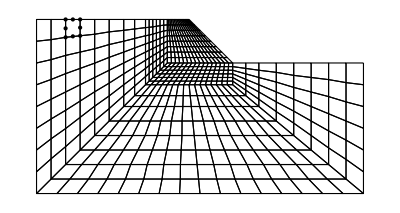

2

{1,2,5,12,17,26,35,48,64,79,100,123,149,178,209,243,278,319,381,466,563,668,803,950,1119,1278,1378,1435,1471,1501,1526,1550,1571}

{1571,1572,1574,1577,1579,1581,1586,1588,1591,1596,1599,1602,1605,1608,1610,1612,1613}

{1,3,6,13,18,29,39,55,70,91,112,139,170}

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["https://www.dropbox.com/s/pyio7qkv52a6n60/mesh-talude-els.txt?dl=1","Table"],1];
nnodesAll=Import["https://www.dropbox.com/s/wkcyf51o1wppmpx/mesh-talude-nodes.txt?dl=1","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=Table[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,8}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Dashing[Tiny]],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];

meshVis2=Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{PointSize[Medium],Black,MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Black,Point[nnodes]}}];
meshVis1=Graphics[{FaceForm[],EdgeForm[Dashing[Tiny]],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
meshVis1=Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{PointSize[Medium],Black,MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Black,Point[nnodes]}}];
el=1;
nodeel=Table[nnodes[[topol[[el]][[i]]]],{i,1,Length[topol[[el]]]}]
nodeVis=Graphics[{PointSize[Medium],Black,{Black,Point[nodeel]}}];
Show[meshVis1,nodeVis]

order=2
serendipity=True;

x0=0.;xf=75;
y0=0;yf=0;
ndivs=10000;
searchpathinferiorline=Flatten[Table[{x,y},{x,x0,xf,(xf-x0)/ndivs},{y,y0,yf,(yf-y0)/ndivs}],1];
x0=0;xf=0.;
y0=0;yf=40;
searchpathleftline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
x0=75;xf=75;
y0=0;yf=30;
searchpathrigthline=Table[{x0,y},{y,y0,yf,(yf-y0)/ndivs}];
idsinferior=FindIds[nnodes,searchpathinferiorline]
idsleft=FindIds[nnodes,searchpathleftline]
idsrigth=FindIds[nnodes,searchpathrigthline]
```

```mathematica
planestress=False;
serendipity=True;
bodyforce=0;
order=2;
eltype=1;


subst2={c->50.,phi->20/180. Pi,young->20000. (*kPa*),nu->0.49,G->young/(2(1+nu)),K->(young)/(3 (1-2nu)),A->3 Tan[phi]/Sqrt[9+12 Tan[phi]^2],
B->3 /Sqrt[9+12 Tan[phi]^2]};


f[x_]:=0;
(*FEXT=ContributeStraigthLineNewman[nnodes,order,idssup,{0,-1},f];*)
bodyforce=20;


globalcounter=1;
intrule=IntegrationRule[order,eltype];
npts=Length[intrule]; 
nglobalpts=Length[topol] npts;
epspvec=Table[0,{nglobalpts},{3}];
epspsolitern=Table[0,{nglobalpts},{3}];

solss={};
sol2={{0,0}};
sol3={};
displace=Table[0,{Length[nnodes] 2}];
AppendTo[solss,displace];
epspsolu={};
stresssolu={};
dgammasol={};
soltalude={};
lamb=1;
diff=10;
l0=0.8;
l=l0
niterdesired=5;
counterout=1;
tol1=10^-6;
tol2=10^-6;
While[Abs[diff]>tol1 && counterout≤80,

Print["i = ",counterout, " | lamb = ",lamb, " | lambn = ",lambn," | diff = ",diff];
counter=1;
err1=10;
err2=10;

dw=Table[0,{Length[nnodes] 2}];

lambn=lamb;
While[counter≤50&& err2>tol2,

epsppost={};
dgamma={};
stressppost={};
globalcounter=1;
{KT,FINT,FEXTB}=Assemble[allcoords,nnodes,topol,order,eltype,displace];
FEXT=FEXTB;
imposex=1;
imposey=2;
R=lamb  FEXT-FINT;
{KT,R}=ContributeLineDirichlet[KT,R,idsinferior,{imposey,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsleft,{imposex,0}];
{KT,R}=ContributeLineDirichlet[KT,R,idsrigth,{imposex,0}];

{KT,FEXT}=ContributeLineDirichlet[KT,FEXT,idsinferior,{imposey,0}];
{KT,FEXT}=ContributeLineDirichlet[KT,FEXT,idsleft,{imposex,0}];
{KT,FEXT}=ContributeLineDirichlet[KT,FEXT,idsrigth,{imposex,0}];

dws=LinearSolve[KT,R,Method->"Banded"];
dwb=LinearSolve[KT,FEXT,Method->"Banded"];;
aa=dwb.dwb;
bb=2(dw+dws).dwb;
ccc=(dw+dws).(dw+dws)-l^2;
(*Print["a = ",aa];
Print["b = ",bb];
Print["c = ",ccc];*)
dlamb=Solve[aa x^2 +bb x+ccc==0,x][[2,1,2]];
dww=dws+dlamb dwb;
dw+=dww;
lamb+=dlamb;
(*dw=LinearSolve[KT,R];*)
res=Norm[dww];
displace+=dww;
err1=Norm[R]/Norm[lamb  FEXT];
(*If[err1>temp && counter>4,diverge=True];*)
temp=err1;
err2=Norm[dww]/Norm[displace];

Print["Iteration number = " ,counter,"  |R|/|FE| =  ",Norm[R]/Norm[lamb FEXT], "  |Δu|/|u| = ",Norm[dww]/Norm[displace],"  |R| =  ",Norm[R] , " |dw| = ",Norm[dww], " | dlamb = ",dlamb, " | lamb = ",lamb, " | bodyforce lamb = ",bodyforce lamb];
counter++;
];
diff=Abs[lamb-lambn];
Print["l = ",l];
AppendTo[stresssolu,stressppost];
AppendTo[dgammasol,dgamma];
AppendTo[epspsolu,epsppost];
AppendTo[solss,displace];
id=FindIds[nnodes,{{35,40}}][[1]];
AppendTo[soltalude,{-displace[[id 2]], lamb}];
AppendTo[sol3,epspvec];

(*Atualiza variável de estado plástica no passo convergido*)
epspsolitern=epspvec;
counterout++;
]
```

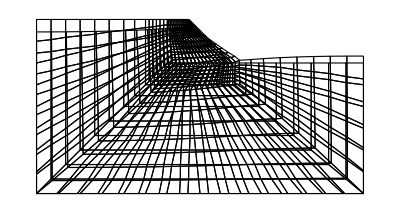

```mathematica
sol=solss[[4]];
scale=5;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=Table[{deformed[[i]],deformed[[i+1]]},{i,1,Length[deformed],2}];
g=Show[meshVis1,Graphics[{FaceForm[],EdgeForm[Black],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}]]
```

```mathematica
(*sol22={{0.015536588936783481,0.17445561056739042},{0.031073177873566928,0.34891122113478046},{0.04661002770689307,0.5233646678076872},{0.06214768189194198,0.6978117907486474},{0.07768899413170943,0.8722358321655745},{0.09324294732694849,1.046592495670614},{0.10884575612764076,1.2206827264075166},{0.12450621116547281,1.394337835385436},{0.14023010404015704,1.5675918151614172},{0.15601382093185917,1.7404712131905544},{0.1718848439416772,1.912842173765331},{0.1878541763043229,2.084441364751228},{0.20394755772901438,2.2552238958690882},{0.22013100233080346,2.4248357800938116},{0.23644857385221718,2.5930130812378973},{0.25292647506293375,2.7603156976394208},{0.2696144496390673,2.9261665737226523},{0.2865478242251344,3.090181739223008},{0.3038549860986469,3.2525580706095596},{0.3216435493707461,3.413373369528334},{0.34008351299066997,3.5724013327856317},{0.3593770702605006,3.7291203744937422},{0.37976332170019256,3.882767126068085},{0.40168143303533993,4.031467320418872},{0.42632017154133056,4.169906365882636},{0.4577659568169417,4.249236439313923},{0.4910098415296757,4.294353072062277},{0.5241078818557257,4.3108476174138675},{0.5569300306918323,4.318778832283308},{0.5896294347343108,4.323882542341687},{0.6222537502042548,4.327678430447161},{0.6548483791115087,4.330679827653437},{0.6874088603413019,4.33316341048473},{0.7199544846215081,4.335259707185451},{0.7524796441873479,4.337072125596248},{0.7849781090488963,4.338654746515468},{0.8174705256628216,4.340060781333659},{0.8499531969333464,4.341333941663544},{0.8824265930388862,4.342479524941415},{0.914894775207239,4.343524418979461},{0.9473517907481463,4.3444836438397365},{0.9798003113499754,4.345372183862315},{1.0122208669448955,4.346192755588693},{1.0445929748200125,4.346897286908888},{1.0770141468097445,4.347714082281084}};*)
```

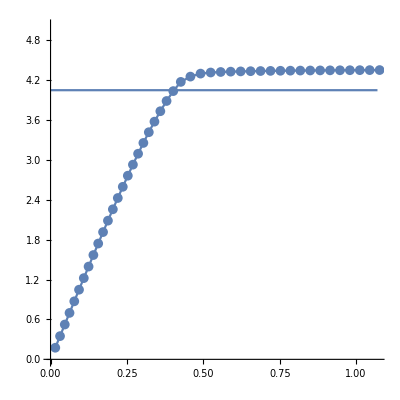

```mathematica
Show[ListLinePlot[soltalude,AspectRatio->1,PlotMarkers->{Automatic, 10}],Plot[4.045,{x,0,1.07}],PlotRange->{{0,1.07},{0,5}}]
```

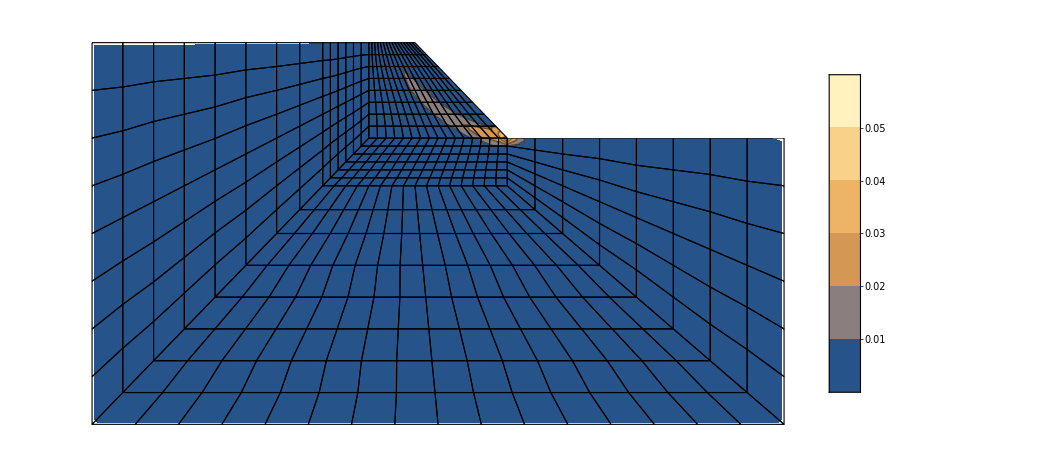

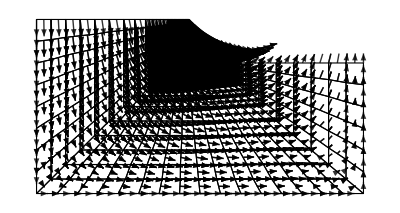

```mathematica
gph=Graphics[{White,Polygon[{{35,40},{45,30},{75,30},{75,40}}]}];
{vecs2,vecs3}=ComputeSolNoInterpolation[topol,nnodes,order,sol,eltype,scale];
arrows=Table[Graphics[{Opacity[0.8],Black,Arrowheads[.012],Arrow[{vecs2[[el]][[i]][[1]],vecs2[[el]][[i]][[2]]}]}],{el,1,Length[vecs2]},{i,1,Length[vecs2[[el]]]}];
teste1=Table[{dgammasol[[25]][[i]][[1]],dgammasol[[25]][[i]][[2]],dgammasol[[25]][[i]][[3]]},{i,1,Length[dgammasol[[25]]]}];
Show[ListContourPlot[teste1,PlotLegends->{Placed[Automatic,{Left,Center}]}],gph,meshVis2,PlotRange->All,AspectRatio->Automatic,Frame->False]
sh=Show[meshVis1,arrows,PlotRange->All]
```